```mathematica
Lx=4;Ly =4;
```

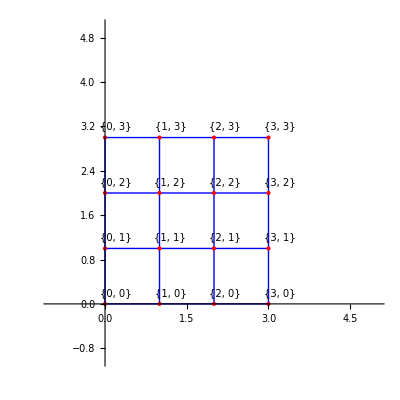

```mathematica
Graphics[
Module[{points,lines},
points=Flatten[Table[{m,n},{m,0,Lx-1},{n,0,Ly-1}],1];
lines=Select[Subsets[points,{2}],ManhattanDistance @@#==1&];
labels=Table[Text[Style[ToString[{m,n}],10],{m+0.2,n+0.2}],{m,0,Lx-1},{n,0,Ly-1}];
{Blue,Line/@ lines,Red, PointSize[Large],Point/@points,Black,Flatten[labels]}
],
Axes -> True,
AxesOrigin->{0,0},
PlotRange->{{-1,Lx+1},{-1,Ly+1}},
AspectRatio->1
]
```

```mathematica
horizontalBonds=Table[{{m,n},{m+1,n}},{m,0,Lx-2},{n,0,Ly-1}];
verticalBonds=Table[{{m,n},{m,n+1}},{m,0,Lx-1},{n,0,Ly-2}];

bonds=Join[Flatten[horizontalBonds,1],Flatten[verticalBonds,1]];
bonds
```

{{{0,0},{1,0}},{{0,1},{1,1}},{{0,2},{1,2}},{{0,3},{1,3}},{{1,0},{2,0}},{{1,1},{2,1}},{{1,2},{2,2}},{{1,3},{2,3}},{{2,0},{3,0}},{{2,1},{3,1}},{{2,2},{3,2}},{{2,3},{3,3}},{{0,0},{0,1}},{{0,1},{0,2}},{{0,2},{0,3}},{{1,0},{1,1}},{{1,1},{1,2}},{{1,2},{1,3}},{{2,0},{2,1}},{{2,1},{2,2}},{{2,2},{2,3}},{{3,0},{3,1}},{{3,1},{3,2}},{{3,2},{3,3}}}

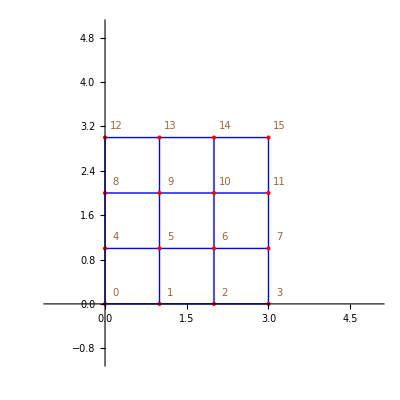

```mathematica
(*Generate lattice points with unique integer labels*)
points=Flatten[Table[{m,n},{n,0,Ly-1},{m,0,Lx-1}],1];


(*Assign an index to each point*)
indexedPoints=AssociationThread[points->Range[0,Length[points]-1]];

(*Horizontal and vertical bonds*)
horizontalBonds=Table[{{m,n},{m+1,n}},{m,0,Lx-2},{n,0,Ly-1}];
verticalBonds=Table[{{m,n},{m,n+1}},{m,0,Lx-1},{n,0,Ly-2}];
bonds=Join[Flatten[horizontalBonds,1],Flatten[verticalBonds,1]];

(*Plot with numbered labels*)
Graphics[{Blue,Line/@bonds,Red,PointSize[Large],Point/@Keys[indexedPoints],Brown,Table[Text[Style[ToString[indexedPoints[{m,n}]],10],{m+0.2,n+0.2}],{m,0,Lx-1},{n,0,Ly-1}]//Flatten},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,Lx+1},{-1,Ly+1}},AspectRatio->1]
```

```mathematica
(*Convert bonds to integer-labeled format*)
indexMap=AssociationThread[points->Range[0,Length[points]-1]];
integerBonds=Sort/@(indexMap/@#&/@bonds);
integerBonds
Length[integerBonds]
```

{{0,1},{4,5},{8,9},{12,13},{1,2},{5,6},{9,10},{13,14},{2,3},{6,7},{10,11},{14,15},{0,4},{4,8},{8,12},{1,5},{5,9},{9,13},{2,6},{6,10},{10,14},{3,7},{7,11},{11,15}}

24

```mathematica
(*periodicity*)
siteIndex[m_,n_]:=Mod[m,Lx]+Lx*Mod[n,Ly];

(*Generates all horizontal or vertical bonds*)
generateBonds[dir_,periodic_]:=Module[{rangeM,rangeN,pairFn},If[dir==="horizontal",rangeM=If[periodic,Range[0,Lx-1],Range[0,Lx-2]];
rangeN=Range[0,Ly-1];
pairFn={siteIndex[#,#2],siteIndex[#+1,#2]}&;,rangeM=Range[0,Lx-1];
rangeN=If[periodic,Range[0,Ly-1],Range[0,Ly-2]];
pairFn={siteIndex[#,#2],siteIndex[#,#2+1]}&;];
Sort/@Flatten[Table[pairFn[m,n],{n,rangeN},{m,rangeM}],1]];

(*Bonds for each case*)
bondsPBCm=Join[generateBonds["horizontal",True],generateBonds["vertical",False]];
bondsPBCn=Join[generateBonds["horizontal",False],generateBonds["vertical",True]];
bondsPBCboth=Join[generateBonds["horizontal",True],generateBonds["vertical",True]];

(*Output*)
Print["PBC in m only:"];
bondsPBCm//Print;
Length[bondsPBCm]//Print;

Print["PBC in n only:"];
bondsPBCn//Print;
Length[bondsPBCn]//Print;

Print["PBC in both m and n:"];
bondsPBCboth//Print;
Length[bondsPBCboth]//Print;
```

PBC in m only:

{{0,1},{1,2},{2,3},{0,3},{4,5},{5,6},{6,7},{4,7},{8,9},{9,10},{10,11},{8,11},{12,13},{13,14},{14,15},{12,15},{0,4},{1,5},{2,6},{3,7},{4,8},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15}}

28

PBC in n only:

{{0,1},{1,2},{2,3},{4,5},{5,6},{6,7},{8,9},{9,10},{10,11},{12,13},{13,14},{14,15},{0,4},{1,5},{2,6},{3,7},{4,8},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15},{0,12},{1,13},{2,14},{3,15}}

28

PBC in both m and n:

{{0,1},{1,2},{2,3},{0,3},{4,5},{5,6},{6,7},{4,7},{8,9},{9,10},{10,11},{8,11},{12,13},{13,14},{14,15},{12,15},{0,4},{1,5},{2,6},{3,7},{4,8},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15},{0,12},{1,13},{2,14},{3,15}}

32